```mathematica
normrnd[mean_, sd_]:=RandomReal[NormalDistribution[mean,sd]]
```

```mathematica
hi1={Table[normrnd[.8,.1],{x,1000}],Table[normrnd[.75,.15],{x,1000}]};
```

```mathematica
hi2={Table[normrnd[.25,.2],{x,1000}],Table[normrnd[.15,.15],{x,1000}]};
```

```mathematica
hi3={Table[normrnd[-.8,.1],{x,1000}],Table[normrnd[-.85,.15],{x,1000}]};
```

```mathematica
hi4={Table[normrnd[-.5,.1],{x,1000}],Table[normrnd[-.45,.15],{x,1000}]};
```

```mathematica
Export["/Users/jinp6301/Dropbox/HotCoCo/testdata1.csv",Transpose[hi1]];
```

```mathematica
Export["/Users/jinp6301/Dropbox/HotCoCo/testdata2.csv",Transpose[hi2]];
```

```mathematica
Export["/Users/jinp6301/Dropbox/HotCoCo/testdata3.csv",Transpose[hi3]];
```

```mathematica
Export["/Users/jinp6301/Dropbox/HotCoCo/testdata4.csv",Transpose[hi4]];
```

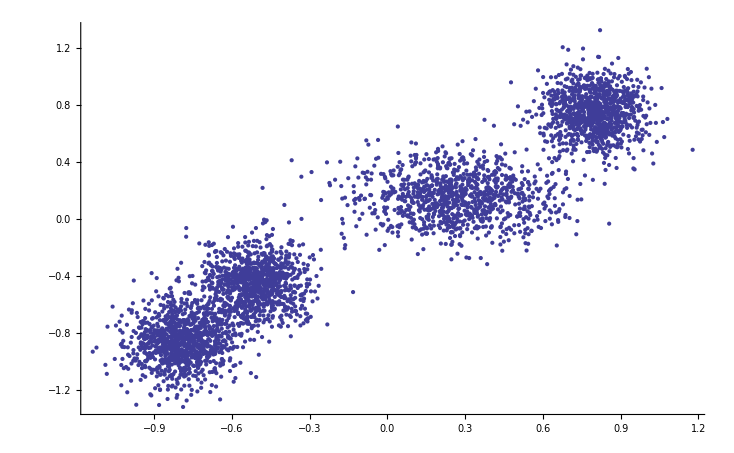

```mathematica
ListPlot[Join[Transpose[hi1],Transpose[hi2],Transpose[hi3],Transpose[hi4]]]
```